```mathematica
dir=NotebookDirectory[];
```

```mathematica
input=Import[dir<>"../input/"<>"07.txt","Text" ];
```

```mathematica
input;
```

```mathematica
inputL=input//StringSplit[#,"\n"]&//Sort;
```

```mathematica
inputL//Take[#,10]&//TableForm
```

Step A must be finished before step K can begin.
Step A must be finished before step L can begin.
Step A must be finished before step O can begin.
Step A must be finished before step X can begin.
Step B must be finished before step Q can begin.
Step B must be finished before step S can begin.
Step B must be finished before step Y can begin.
Step C must be finished before step L can begin.
Step D must be finished before step K can begin.
Step D must be finished before step L can begin.

```mathematica
inputL//Length
```

101

```mathematica
inputL[[5]]
```

Step B must be finished before step Q can begin.

```mathematica
inputL[[5]]//StringSplit[#,{" "}]&//{#[[2]],#[[8]]}&
```

{B,Q}

```mathematica
inputE=StringSplit[#,{" "}]&/@inputL//{#[[2]],#[[8]]}&/@#&
```

{{A,K},{A,L},{A,O},{A,X},{B,Q},{B,S},{B,Y},{C,L},{D,K},{D,L},{D,O},{D,T},{E,K},{E,L},{E,Y},{F,A},{F,I},{F,L},{F,Q},{F,R},{F,T},{F,V},{F,Z},{G,C},{G,F},{G,M},{G,P},{G,X},{G,Z},{H,R},{H,T},{H,X},{I,K},{I,O},{I,R},{I,S},{I,Z},{J,E},{J,F},{J,H},{J,K},{J,N},{J,W},{L,O},{L,R},{L,S},{L,X},{M,D},{M,H},{M,I},{M,O},{M,U},{M,Z},{N,B},{N,C},{N,I},{N,L},{N,X},{O,K},{O,R},{P,O},{P,R},{P,X},{P,Z},{Q,K},{Q,O},{Q,P},{Q,S},{Q,X},{R,K},{S,K},{S,O},{S,P},{S,X},{S,Z},{T,Q},{T,R},{U,L},{U,O},{U,R},{U,S},{U,X},{V,A},{V,E},{V,O},{V,P},{V,T},{V,U},{V,Z},{W,E},{W,Q},{W,X},{X,K},{X,O},{X,R},{X,Z},{Y,A},{Y,X},{Y,Z},{Z,K},{Z,O}}

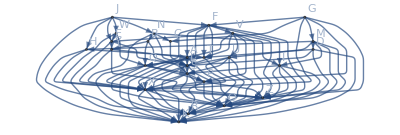

```mathematica
graph=#[[1]]->#[[2]]&/@inputE//Graph[#,VertexLabels->"Name"]&
```

```mathematica
graph//TopologicalSort//StringJoin@@#&
```

GMDJWNCBHFVUTQEYALISPXZORK

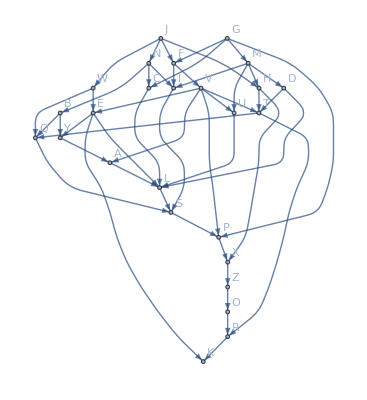

```mathematica
g=graph//TransitiveReductionGraph;g//Graph[#,VertexLabels->"Name"]&
```

```mathematica
s1=Select[VertexList@g,VertexInDegree[g,#]==0&]
```

{G,J}

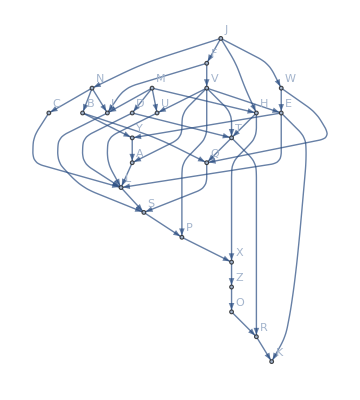

```mathematica
g=VertexDelete[g,"G"]//Graph[#,VertexLabels->"Name"]&
```

```mathematica
s2=Select[VertexList@g,VertexInDegree[g,#]==0&]//Sort
```

{J,M}

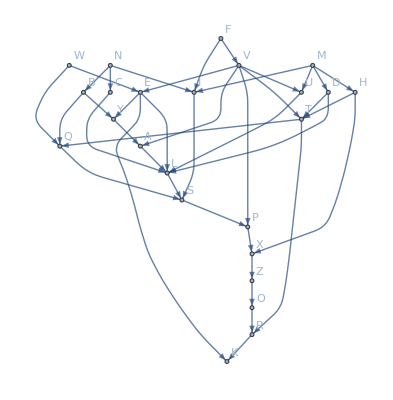

```mathematica
g=VertexDelete[g,"J"]//Graph[#,VertexLabels->"Name"]&
```

```mathematica
Select[VertexList@g,VertexInDegree[g,#]==0&]//Sort
```

{F,M,N,W}

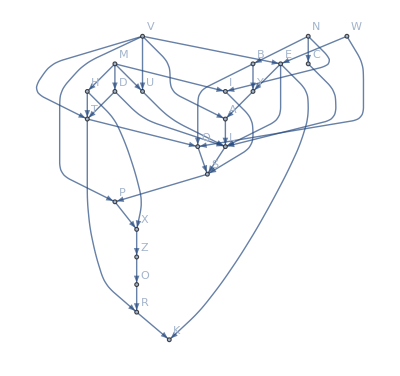

```mathematica
g=VertexDelete[g,"F"]//Graph[#,VertexLabels->"Name"]&
```

```mathematica
Select[VertexList@g,VertexInDegree[g,#]==0&]//Sort
```

{M,N,V,W}

```mathematica
TopSort[graph_]:=Block[{g=graph,sol={},e,s},
While[VertexList@g≠{},
s=Select[VertexList@g,VertexInDegree[g,#]==0&]//Sort;
e=First@s;
AppendTo[sol,e];
g=VertexDelete[g,e]
(*Print[g//Graph[#,VertexLabels->"Name"]&];*)
];
sol
]
```

```mathematica
sol1=TopSort[graph2]//StringJoin@@#&
```

GJFMDHNBCIVTUWEQYALSPXZORK

```mathematica
alpha=ToUpperCase@Alphabet[]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

```mathematica
costs=#->First[ToCharacterCode[#]-ToCharacterCode["A"]+61]&/@alpha
```

{A→61,B→62,C→63,D→64,E→65,F→66,G→67,H→68,I→69,J→70,K→71,L→72,M→73,N→74,O→75,P→76,Q→77,R→78,S→79,T→80,U→81,V→82,W→83,X→84,Y→85,Z→86}

```mathematica
paths=FindPath[graph2,"J","K",Infinity,All];paths//TableForm
```

J | W | E | K |  |  |  |  |  |  |  |  |  | 
J | H | T | R | K |  |  |  |  |  |  |  |  | 
J | F | V | E | K |  |  |  |  |  |  |  |  | 
J | F | V | T | R | K |  |  |  |  |  |  |  | 
J | H | X | Z | O | R | K |  |  |  |  |  |  | 
J | F | V | P | X | Z | O | R | K |  |  |  |  | 
J | W | Q | S | P | X | Z | O | R | K |  |  |  | 
J | N | I | S | P | X | Z | O | R | K |  |  |  | 
J | F | I | S | P | X | Z | O | R | K |  |  |  | 
J | W | E | L | S | P | X | Z | O | R | K |  |  | 
J | N | C | L | S | P | X | Z | O | R | K |  |  | 
J | N | B | Q | S | P | X | Z | O | R | K |  |  | 
J | H | T | Q | S | P | X | Z | O | R | K |  |  | 
J | F | V | U | L | S | P | X | Z | O | R | K |  | 
J | F | V | E | L | S | P | X | Z | O | R | K |  | 
J | F | V | T | Q | S | P | X | Z | O | R | K |  | 
J | F | V | A | L | S | P | X | Z | O | R | K |  | 
J | W | E | Y | A | L | S | P | X | Z | O | R | K | 
J | N | B | Y | A | L | S | P | X | Z | O | R | K | 
J | F | V | E | Y | A | L | S | P | X | Z | O | R | K

```mathematica
paths//.costs//Plus@@@#&//Last
```

1050

```mathematica
FindPath[graph2,"G","K",Infinity,All]//.costs//Plus@@@#&//Last
```

1047

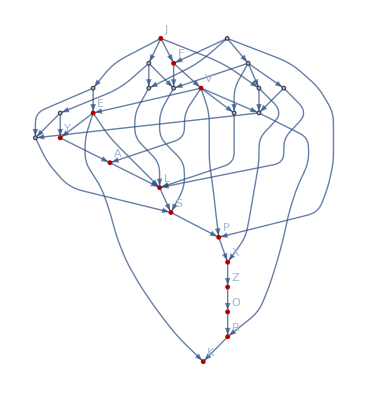

```mathematica
HighlightGraph[graph2,PathGraph[Last@paths],VertexLabels->"Name"]
```